# Plotting projected (electronic) DOS from different DFT codes for Spin-polarized systems

```mathematica
(* a way to lower down the amount of memory *)
$HistoryLength=2;
```

```mathematica
(* for path checking *)
atomicprop=Import[NotebookDirectory[]<>"/atomic_prop.dat","Table"];
path="~/Documents/WORK/z-sshfs/Tarkil/FePc_Gr/B3LYP_light_triplet_opt/";
geom=(*Import[path<>"CONTCAR","Table"];*) (*Not necessary, working for VASP only *)  Import[path<>"geometry.in","Table"];(*Not necessary, working for FHI-AIMS only *)
(*maxat1=geom[[1,1]]*) (* This is not neccessary for plotting *)
geom[[Range[1,20],All]]//TableForm  (* Just to show sample*)
```

# |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
# | This | is | the | geometry | file | that | corresponds | to | the | current | relaxation | step. |  |  |  | 
# | If | you | do | not | want | this | file | to | be | written, | set | the | write_restart_geometry | flag | to | .false.
# |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
#lattice_vector | 25. | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  | 
#lattice_vector | 0. | 25. | 0. |  |  |  |  |  |  |  |  |  |  |  |  | 
#lattice_vector | 0. | 0. | 30. |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
atom | 0.0284003 | 0.02187 | 0.041695 | Fe |  |  |  |  |  |  |  |  |  |  |  | 
initial_moment | 2 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
atom | 2.40735 | 2.39616 | 0.0447131 | N |  |  |  |  |  |  |  |  |  |  |  | 
atom | 2.40293 | -2.3573 | 0.0392894 | N |  |  |  |  |  |  |  |  |  |  |  | 
atom | -2.35053 | -2.35245 | 0.0393962 | N |  |  |  |  |  |  |  |  |  |  |  | 
atom | -2.34614 | 2.40103 | 0.0444867 | N |  |  |  |  |  |  |  |  |  |  |  | 
atom | 1.9722 | 0.0198406 | 0.0415883 | N |  |  |  |  |  |  |  |  |  |  |  | 
atom | 2.77976 | -1.09585 | 0.0404222 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 2.78182 | 1.13406 | 0.0430279 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 4.17018 | -0.681632 | 0.0408123 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 4.17141 | 0.717381 | 0.0424132 | C |  |  |  |  |  |  |  |  |  |  |  | 
atom | 5.35837 | -1.40453 | 0.0402035 | C |  |  |  |  |  |  |  |  |  |  |  |

## VAPS spin-polarized

```mathematica
list=Table[i,{i,1,57,1}];
pathse=(*path*)"~/Documents/WORK/z-sshfs/Tarkil/CuPc_SnSi/PBE+U_VASP/";doscar1=Import[pathse<>"DOSCAR","Table"];
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].(*{1,0,0,0,0,0,0,0,0,0}*){1,0,0,0,0,0,0},dos01[i].(*{0,1,1,1,1,1,1,1,1,1}*){0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].(*{1,0,0,0,0,0,0,0,0,0}*){1,0,0,0,0,0,0},dos01[i].(*{0,1,1,1,1,1,1,1,1,1}*){0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spd division only LORBIT=10*)
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spxpy... division - LORBIT = 11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];
dosup1=dosesmolup2;dosdn1=dosesmoldn2;
```

-4.07295

```mathematica
list=Table[i,{i,1,57,1}];
pathse=(*path*)"~/Documents/WORK/z-sshfs/Tarkil/CuPc_SnSi/4L_VASP/1Si_SnSi_CuPc_2/";doscar1=Import[pathse<>"DOSCAR","Table"];
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].(*{1,0,0,0,0,0,0,0,0,0}*){1,0,0,0,0,0,0},dos01[i].(*{0,1,1,1,1,1,1,1,1,1}*){0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].(*{1,0,0,0,0,0,0,0,0,0}*){1,0,0,0,0,0,0},dos01[i].(*{0,1,1,1,1,1,1,1,1,1}*){0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spd division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spxpy... division LORBIT=11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];
dosup2=dosesmolup2;dosdn2=dosesmoldn2;
```

-1.16334

```mathematica
list=Table[i,{i,1,57,1}];
pathse=(*path*)"~/Documents/WORK/z-sshfs/Tarkil/CuPc_SnSi/4L_VASP/1Si_SnSi_CuPc_3/";doscar1=Import[pathse<>"DOSCAR","Table"];
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].(*{1,0,0,0,0,0,0,0,0,0}*){1,0,0,0,0,0,0},dos01[i].(*{0,1,1,1,1,1,1,1,1,1}*){0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].(*{1,0,0,0,0,0,0,0,0,0}*){1,0,0,0,0,0,0},dos01[i].(*{0,1,1,1,1,1,1,1,1,1}*){0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spd division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spxpy... division LORBIT=11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];dosup3=dosesmolup2;dosdn3=dosesmoldn2;
```

-1.17503

```mathematica
list=Table[i,{i,1,57,1}];
pathse=(*path*)"~/Documents/WORK/z-sshfs/Tarkil/CuPc_SnSi/4L_VASP/1Si_SnSi_CuPc_Pavel/";doscar1=Import[pathse<>"DOSCAR","Table"];
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].(*{1,0,0,0,0,0,0,0,0,0}*){1,0,0,0,0,0,0},dos01[i].(*{0,1,1,1,1,1,1,1,1,1}*){0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].(*{1,0,0,0,0,0,0,0,0,0}*){1,0,0,0,0,0,0},dos01[i].(*{0,1,1,1,1,1,1,1,1,1}*){0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spd division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spxpy... division LORBIT=11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];dosup4=dosesmolup2;dosdn4=dosesmoldn2;
```

-1.18723

## FHI-AIMS spin-polarized

```mathematica
shift=0.0;
list=Table[i,{i,1,57,1}];
j=2;  (* All orbitals: j=2; s-orb.08: j=3; p-orb: j=4; d-orb: j=5;*)
path0=path; (*"~/Documents/WORK/z-sshfs/Tarkil/FePc_Gr/B3LYP_light_triplet_opt/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.; (* possible error: Part::partw: "Part [i,1] of ... does not exist.", it has no effect on functionality*)
tmp2=Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosdn1=tmp2[[All,{1,2}]];
tmp2=.;dosdn1[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn1]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}]
dosdn1[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosdn1[[All,2]]*=-1;
dosdn1=Inner[Plus,dosdn1,{shift,0},List];

tmp2=Import[path0<>"atom_proj_dos_spin_up"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosup1=tmp2[[All,{1,2}]];
tmp2=.;dosup1[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn1]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}];dosup1[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosup1=Inner[Plus,dosup1,{shift,0},List];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
shift=0.0;

list=(*Table[i,{i,1,57,1}]*){1};
j=5;  (* All orbitals: j=2; s-orb.08: j=3; p-orb: j=4; d-orb: j=5;*)
path0=path; (*"~/Documents/WORK/z-sshfs/Tarkil/FePc_Gr/B3LYP_light_triplet_opt/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.; (* possible error: Part::partw: "Part [i,1] of ... does not exist.", it has no effect on functionality*)
tmp2=Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosdn2=tmp2[[All,{1,2}]];
tmp2=.;dosdn2[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn2]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}]
dosdn2[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosdn2[[All,2]]*=-1;
dosdn2=Inner[Plus,dosdn2,{shift,0},List];

tmp2=Import[path0<>"atom_proj_dos_spin_up"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosup2=tmp2[[All,{1,2}]];
tmp2=.;dosup2[[All,2]]=0.0;null=Table[0.0,{i,Length[dosup2]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}];dosup2[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosup2=Inner[Plus,dosup2,{shift,0},List];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
shift=0.0;

list=(*Table[i,{i,1,57,1}]*){1};
j=2;  (* All orbitals: j=2; s-orb.08: j=3; p-orb: j=4; d-orb: j=5;*)
path0=path; (*"~/Documents/WORK/z-sshfs/Tarkil/FePc_Gr/B3LYP_light_triplet_opt/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.; (* possible error: Part::partw: "Part [i,1] of ... does not exist.", it has no effect on functionality*)
tmp2=Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosdn3=tmp2[[All,{1,2}]];
tmp2=.;dosdn3[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn3]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}]
dosdn3[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosdn3[[All,2]]*=-1;
dosdn3=Inner[Plus,dosdn3,{shift,0},List];

tmp2=Import[path0<>"atom_proj_dos_spin_up"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosup3=tmp2[[All,{1,2}]];
tmp2=.;dosup3[[All,2]]=0.0;null=Table[0.0,{i,Length[dosup3]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}];dosup3[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosup3=Inner[Plus,dosup3,{shift,0},List];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
shift=0.0;

list=(*Table[i,{i,1,57,1}]*){1};
j=4;  (* All orbitals: j=2; s-orb.08: j=3; p-orb: j=4; d-orb: j=5;*)
path0=path; (*"~/Documents/WORK/z-sshfs/Tarkil/FePc_Gr/B3LYP_light_triplet_opt/";*)
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.; (* possible error: Part::partw: "Part [i,1] of ... does not exist.", it has no effect on functionality*)
tmp2=Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosdn4=tmp2[[All,{1,2}]];
tmp2=.;dosdn4[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn4]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}]
dosdn4[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosdn4[[All,2]]*=-1;
dosdn4=Inner[Plus,dosdn4,{shift,0},List];

tmp2=Import[path0<>"atom_proj_dos_spin_up"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosup4=tmp2[[All,{1,2}]];
tmp2=.;dosup4[[All,2]]=0.0;null=Table[0.0,{i,Length[dosup4]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}];dosup4[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dd[i]=.},{i,list}];
dosup4=Inner[Plus,dosup4,{shift,0},List];
```

Part::partw: Part 1 of {} does not exist.

## Plotting

```mathematica
(* Definitions *)
```

```mathematica
doublestyle={Directive[Thick,Darker[Orange,.0]],Directive[Thick,Darker[Orange,.1]],Directive[Thick,Darker[Orange,.2]],Directive[Thick,Darker[Orange,.3]],Directive[Thick,Darker[Blue,.0]],Directive[Thick,Darker[Blue,.1]],Directive[Thick,Darker[Blue,.2]],Directive[Thick,Darker[Blue,.3]],Directive[Thick,Darker[Blue,.4]],Directive[Thick,Darker[Red,.0]],Directive[Thick,Darker[Green,.0]],Directive[Thick,Darker[Green,.1]],Directive[Thick,Darker[Green,.2]],Directive[Thick,Darker[Green,.3]],Directive[Thick,Darker[Green,.4]],Directive[Thick,Darker[Red,.4]]};
```

```mathematica
doublestyle=Table[Directive[Thick,ColorData[97,"ColorList"][[Quotient[i,2]]]],{i,2,20}];
```

```mathematica
doublestyle=Table[Directive[Thick,ColorData[90,"ColorList"][[Quotient[i,2]]]],{i,2,20}];
```

```mathematica
colordata={Red,Black,Blue,Orange,White};
doublestyle=Table[Directive[Thick,colordata[[Quotient[i,2]]]],{i,2,10}];
```

```mathematica
(* Now the real plotting *)
```

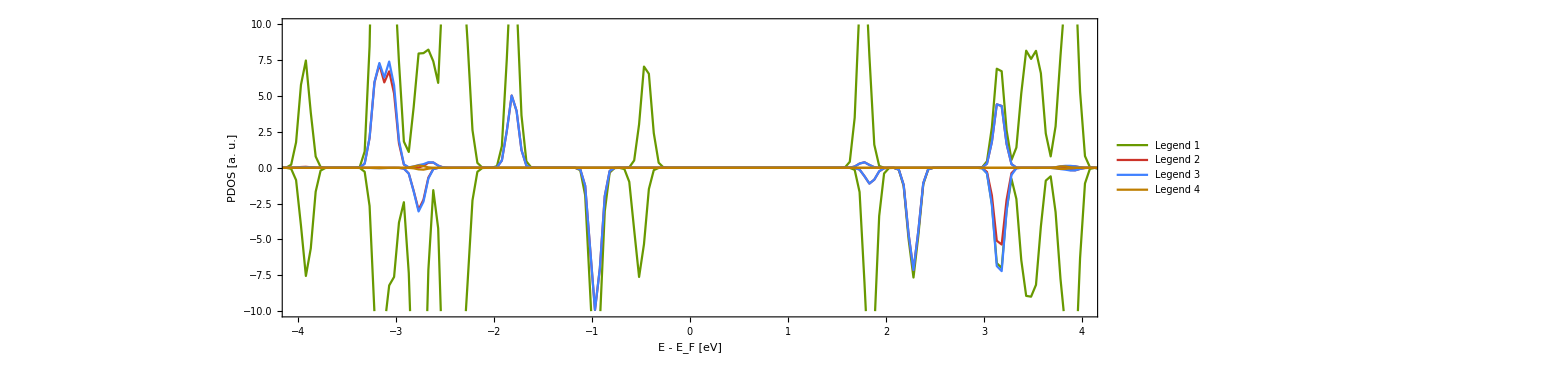

```mathematica
range=10;
jj=ListPlot[{dosup1,dosdn1,dosup2,dosdn2,dosup3,dosdn3,dosup4,dosdn4},Joined->True,PlotRange->{{-4,4},{-range,range}},PlotStyle->doublestyle,Axes->{True,True},AxesStyle->AbsoluteThickness[2],AxesLabel->{,Style["Fermi Level",20,Black]},AxesOrigin->{0,0},Frame->True,FrameLabel->{"E - E_F [eV]"(*" E [eV]"*),"PDOS [a. u.]"},FrameStyle->Directive[Black,AbsoluteThickness[2],20],ImageSize->1500,AspectRatio->1/4,PlotLegends->Placed[LineLegend[{"Legend 1",None,"Legend 2",None,"Legend 3",None,"Legend 4"},LegendLabel->None,LabelStyle->{Darker[Gray,0.7],FontSize->20},LegendFunction->None],(*{.66-0.24,.69+0.15}*)Right]]
```

```mathematica
Export[path<>"dos_molecules_new_models_spinpol.png",jj,Background->None]
```

## VASP spin-orbit coupling

```mathematica
(*  Here, the whole reading take much much longer, therefore it is better to read each directory or list of atoms differently and then assign the DOS to variables once it is completely readed *)
```

```mathematica
list=(*Table[i,{i,1,57,1}];*){1};
pathse=(*path;*)"~/Documents/WORK/z-sshfs/Tarkil/CuPc_SnSi/PBE+U_VASP_so/";
doscar1=Import[pathse<>"DOSCAR","Table"];
doscar1[[Range[1,7]]];
noat=doscar1[[1,1]];
nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];
fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{
dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,1,0,0,0,1,0,0,0,1,0,0}}],dosesmi[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,0,1,0,0,0,1,0,0,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,0,0,1,0,0,0,1,0,0,0,1}}],
dosesall[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,0,0,1,0,0,0,1,0,0,0}}],dos01[i]=.}];*)
For[i=1,i≤noat,i++,{
dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0}}],
dosesmi[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1}}],
dosesall[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0}}],dos01[i]=.}];
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
dosesmolmi=Array[Null,{nosteps,2}];
dosesmolmi[[All,1]]=dostot[[All,1]];
dosesmolall=Array[Null,{nosteps,2}];
dosesmolall[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,
dosesmolmi[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolmi[[i,2]]=dosesmolmi[[i,2]]+dosesmi[list[[j]]][[i,2]]],
dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]],
dosesmolall[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolall[[i,2]]=dosesmolall[[i,2]]+dosesall[list[[j]]][[i,2]]]}];
(*fermi=Import[pathse<>"fermi.dat"][[1,3]]*)
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmolmi2=Inner[Plus,dosesmolmi,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolall2=Inner[Plus,dosesmolall,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]];
dosesmolmi2[[1,2]]=dosesmolmi2[[2,2]];
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];
dosesmolall2[[1,2]]=dosesmolall2[[2,2]];
```

-4.07159

```mathematica
(* Here follows the assigning to plottable variables *)
```

```mathematica
dosup1=dosesmolup2;dosmi1=dosesmolmi2;dosdn1=dosesmoldn2;dosall1=dosesmolall2;
```

```mathematica
dosup2=dosesmolup2;dosmi2=dosesmolmi2;dosdn2=dosesmoldn2;dosall2=dosesmolall2;
```

```mathematica
dosup3=dosesmolup2;dosmi3=dosesmolmi2;dosdn3=dosesmoldn2;dosall3=dosesmolall2;
```

```mathematica
dosup4=dosesmolup2;dosmi4=dosesmolmi2;dosdn4=dosesmoldn2;dosall4=dosesmolall2;
```

```mathematica
(* For possible shifting of the Fermi Level *)
shift=-0.150
dosup1[[All,1]]+=shift;
dosmi1[[All,1]]+=shift;
dosdn1[[All,1]]+=shift;
dosall1[[All,1]]+=shift;

(*dosup2[[All,1]]+=shift;
dosmi2[[All,1]]+=shift;
dosdn2[[All,1]]+=shift;
dosall2[[All,1]]+=shift;

dosup3[[All,1]]+=shift;
dosmi3[[All,1]]+=shift;
dosdn3[[All,1]]+=shift;
dosall3[[All,1]]+=shift;

dosup4[[All,1]]+=shift;
dosmi4[[All,1]]+=shift;
dosdn4[[All,1]]+=shift;
dosall4[[All,1]]+=shift;*)
```

-0.15

## Plotting: Spin-orbit coupling

```mathematica
(* Definitions *)
```

```mathematica
sostyle=Table[Directive[Thick,ColorData[97,"ColorList"][[Quotient[i,3]]]],{i,3,3*10}];
```

```mathematica
colordata={Red,Green,Blue,Orange};
sostyle=Table[Directive[Thick,colordata[[i]]],{i,Length[colordata]}];
```

```mathematica
sostyle={Thick,Thick,Thick,Thick,Directive[Thick,Dashed,ColorData[97][1]],Directive[Thick,Dashed,ColorData[97][2]],Directive[Thick,Dashed,ColorData[97][3]],Directive[Thick,Dashed,ColorData[97][4]]};
```

```mathematica
(* Now the real plotting *)
```

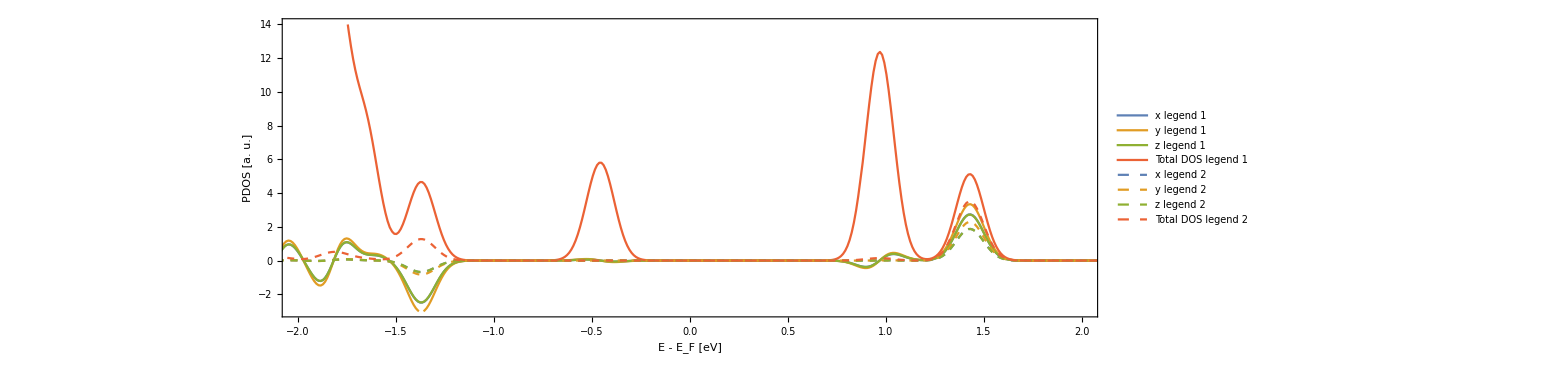

```mathematica
rangedn=3.;rangeup=14.;
jj=ListPlot[{dosup1,dosmi1,dosdn1,dosall1,dosup2,dosmi2,dosdn2,dosall2},Joined->True,PlotRange->{{-2,2},{-rangedn,rangeup}},PlotStyle->sostyle,Axes->{True,True},AxesStyle->AbsoluteThickness[2],AxesLabel->{,Style["Fermi Level",20,Black]},AxesOrigin->{0,0},Frame->True,FrameLabel->{"E - E_F [eV]"(*" E [eV]"*),"PDOS [a. u.]"},FrameStyle->Directive[Black,AbsoluteThickness[2],20],ImageSize->1500,AspectRatio->1/4,PlotLegends->Placed[LineLegend[{"x legend 1","y legend 1","z legend 1","Total DOS legend 1","x legend 2","y legend 2","z legend 2","Total DOS legend 2","x legend 3","y legend 3","z legend 3","Total DOS legend 3","x legend 4","y legend 4","z legend 4","Total DOS legend 4"},LegendLabel->None,LabelStyle->{Darker[Gray,0.7],FontSize->20},LegendFunction->None],(*{.66-0.24,.69+0.15}*)Right]]
```

```mathematica
Export[path<>"dos_spin-orbit.png",jj,Background->None]
```

## Mouse tracking

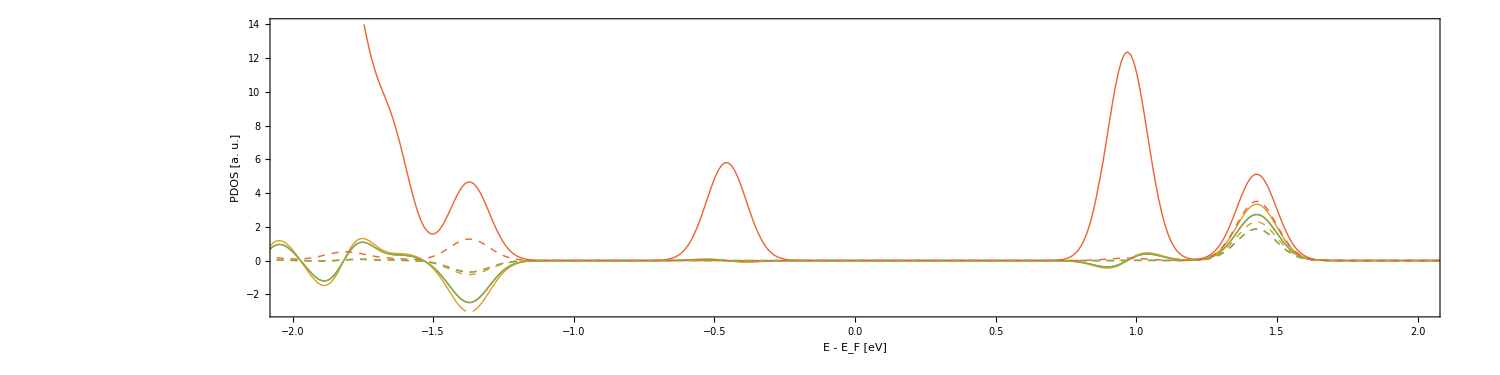
```mathematica
{-Graphics-,Dynamic[MousePosition["Graphics"]]}
```

## View

```mathematica
atomicprop=Import[NotebookDirectory[]<>"/atomic_prop.dat","Table"];
path="~/Documents/WORK/z-sshfs/tmp/VASP/";
filename="CONTCAR"; (* "bas","xyz","in" and CONTCAR/POSCAR files are supported at the moment *)
geomin= Import[path<>filename,"Table"];
geomin[[Range[1,20]]]//TableForm (* Just to see an example *)
```

~/Documents/WORK/z-sshfs/tmp/Fireball/

```mathematica
(* geometry parser *)
If[StringTake[filename,-3]=="bas",{Print["BAS file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=2,i≤maxat1+1,i++,geom[[i-1]]={geomin[[i,1]],atomicprop[[geomin[[i,1]],1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[geomin[[i,1]],2]],atomicprop[[geomin[[i,1]],4]],atomicprop[[geomin[[i,1]],5]],atomicprop[[geomin[[i,1]],6]];}];};,
If[StringTake[filename,-3]=="xyz",{Print["XYZ file"];maxat1=geomin[[1,1]];
geom=Array[Null,{maxat1,9}];
For[i=3,i≤maxat1+2,i++,For[j=1,j≤99,j++,If[ToString[geomin[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i-2]]={j,geomin[[i,1]],geomin[[i,2]],geomin[[i,3]],geomin[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]==".in",{Print["FHI-AIMS in file"];aimsimport2=Array[Null,Length[geomin]];ia=1;cell={};
For[i=1,i≤Length[aimsimport2],i++,If[geomin[[i,1]]=="atom",{aimsimport2[[ia]]=geomin[[i]],ia=ia+1},If[geomin[[i,1]]=="lattice_vector",cell=Append[cell,geomin[[i,{2,3,4}]]]]]];
aimsimport2=Drop[aimsimport2,-Length[geomin]+ia-1];If[cell=={},cell=.];
xyzEx=aimsimport2[[All,{5,2,3,4}]];(*geomin=.;*)aimsimport2=.;
maxat1=Length[xyzEx];
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,For[j=1,j≤Length[atomicprop],j++,If[ToString[xyzEx[[i,1]]]==ToString[atomicprop[[j,1]]],geom[[i]]={j,xyzEx[[i,1]],xyzEx[[i,2]],xyzEx[[i,3]],xyzEx[[i,4]],atomicprop[[j,2]],atomicprop[[j,4]],atomicprop[[j,5]],atomicprop[[j,6]]};]]];};,
If[StringTake[filename,-3]=="CAR",{Print["CONTCAR/POSCAR VASP file"],(*VASP CONTCAR file *)direct=False;
If[geomin[[8,1]]=="Direct",{Print[".1dOK"],tmpn=8,direct=True},If[geomin[[9,1]]=="Direct",{Print[".1dOK"],tmpn=9,direct=True},
If[geomin[[8,1]]=="Cartesian",{Print[".1dOK"],tmpn=8},If[geomin[[9,1]]=="Cartesian",{Print[".1dOK"],tmpn=9},
{Print["problem: geomin[[8,1] = "]<>geomin[[8,1]],Print["problem: geomin[[9,1] = "]<>geomin[[9,1]]}]]]];
tmpn;cell=geomin[[{3,4,5}]];elem=geomin[[6]];
elnum=Length[elem];elemdic=Table[,{i,elnum}];atnum=geomin[[7]];
maxat1=Sum[atnum[[i]],{i,elnum}];atsum=Table[Sum[atnum[[i]],{i,j}],{j,1,elnum}];
For[i=1,i≤elnum,i++,For[j=1,j≤99,j++,If[ToString[elem[[i]]]==ToString[atomicprop[[j,1]]],elemdic[[i]]=j]]];elemdic;
geom=Array[Null,{maxat1,9}];
For[i=1,i≤maxat1,i++,{For[j=1,j≤elnum,j++,If[i≤atsum[[j]],{tmp=j,Break[]}]],k=elemdic[[tmp]],geom[[i]]={k,elem[[tmp]],geomin[[i+tmpn,1]],geomin[[i+tmpn,2]],geomin[[i+tmpn,3]],atomicprop[[k,2]],atomicprop[[k,4]],atomicprop[[k,5]],atomicprop[[k,6]]};};];
If[direct,geom[[All,{3,4,5}]]=geom[[All,{3,4,5}]].cell];},{Print["Unknown Format"]}]]]].1c
```

```mathematica
(* CONTINUATION of geometry reading and plotting *)
rescale = 0.2;
balls=Table[Tooltip[{RGBColor[geom[[i,{7,8,9}]]/256],Sphere[geom[[i,{3,4,5}]],rescale*geom[[i,6]]]},{i,geom[[i,{2,3,4,5}]]}],{i,1,maxat1}];
resbond=1.2;bond=.1;

geom2 = Array[Null, {(maxat1^2), 12}];
k1 = 1;
For[i = 1, i ≤maxat1 , i++, For[j = 1, j < i, j++, If[Norm[geom[[i,{3,4,5}]]-geom[[j,{3,4,5}]]]<= (atomicprop[[geom[[i, 1]], 3]]*resbond + atomicprop[[geom[[j, 1]], 3]]*resbond), {geom2[[k1, {1,2,3,7,8,9}]] =geom[[i,{ 3,4,5,7,8,9}]], geom2[[k1, {4,5,6,10,11,12}]] =geom[[j,{ 3,4,5,7,8,9}]], k1 = k1 + 1}]]];
geom2=Drop[geom2,k1-1-(maxat1^2)];
sticks=Table[Tube[{geom2[[i,{1,2,3}]],geom2[[i,{4,5,6}]]},bond,VertexColors->{RGBColor[geom2[[i,{7,8,9}]]/256],RGBColor[geom2[[i,{10,11,12}]]/256]}],{i,1,Length[geom2],1}];
```

```mathematica
Graphics3D[{balls,sticks},Lighting->"Neutral",ViewPoint->20000. {0,-1,0.1},ImageSize-> 300,Axes->False,Boxed-> False,Background->None]
```

-Graphics3D-

VASP & FHI-AIMS spin-polarized

```mathematica
(* VASP spin-polarized*)
list=Table[i,{i,1,maxat1,1}];
pathse=path;doscar1=Import[pathse<>"DOSCAR","Table"];
(*doscar1[[Range[1,7]]]*)noat=doscar1[[1,1]];nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].(*{1,0,0,0,0,0,0,0,0,0}*){1,0,0,0,0,0,0},dos01[i].(*{0,1,1,1,1,1,1,1,1,1}*){0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].(*{1,0,0,0,0,0,0,0,0,0}*){1,0,0,0,0,0,0},dos01[i].(*{0,1,1,1,1,1,1,1,1,1}*){0,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];(* spd division only LORBIT=10*)
(*For[i=1,i≤noat,i++,{dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1}}](*,Print[i]*),dos01[i]=.}];*)(* spxpy... division - LORBIT = 11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]]}];
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]]; (* 1st energy is always wrong *)
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];
dosup1=dosesmolup2;dosdn1=dosesmoldn2;
```

-1.16334

```mathematica
(* FHI-AIMS spin-polarized*)
shift=0.0;
list=Table[i,{i,1,maxat1,1}];
j=2;  (* All orbitals: j=2; s-orb.08: j=3; p-orb: j=4; d-orb: j=5;*)
path0=path;
tmp1=Import[path0<>"geometry.in","Table"];bas1={};a0=0;
For[i=1,i≤Length[tmp1],i++,If[tmp1[[i,1]]=="atom",{bas1=Append[bas1,{tmp1[[i,5]],tmp1[[i,2]],tmp1[[i,3]],tmp1[[i,4]]}],a0+=1}]];tmp1=.; (* possible error: Part::partw: "Part [i,1] of ... does not exist.", it has no effect on functionality*)
tmp2=Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosdn1=tmp2[[All,{1,2}]];
tmp2=.;dosdn1[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn1]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_dn"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}]
dosdn1[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dosesdn[i]=dd[i],dd[i]=.},{i,list}];
dosdn1[[All,2]]*=-1;
dosdn1=Inner[Plus,dosdn1,{shift,0},List];

tmp2=Import[path0<>"atom_proj_dos_spin_up"<>bas1[[1,1]]<>"0001.dat","Table",HeaderLines->4];dosup1=tmp2[[All,{1,2}]];
tmp2=.;dosup1[[All,2]]=0.0;null=Table[0.0,{i,Length[dosdn1]}];
Do[{dd[i]=If[i<10,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"000"<>ToString[i]<>".dat","Table",HeaderLines->4],If[i<100,Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"00"<>ToString[i]<>".dat","Table",HeaderLines->4],Import[path0<>"atom_proj_dos_spin_up"<>bas1[[i,1]]<>"0"<>ToString[i]<>".dat","Table",HeaderLines->4]]],If[bas1[[i,1]]=="H",{dd[i]=MapThread[Append,{dd[i],null}]}]},{i,list}];dosup1[[All,2]]=Sum[dd[i][[All,j]],{i,list}];Do[{dosesup[i]=dd[i],dd[i]=.},{i,list}];
dosup1=Inner[Plus,dosup1,{shift,0},List];
```

Part::partw: Part 1 of {} does not exist.

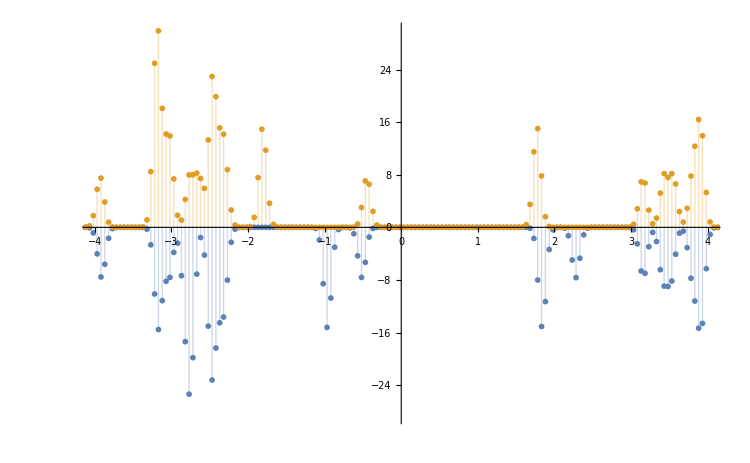

```mathematica
ListPlot[{Table[Tooltip[dosdn1[[i]],i],{i,1,Length[dosdn1]}],Table[Tooltip[dosup1[[i]],i],{i,1,Length[dosup1]}]},Filling->Axis,Joined->False,PlotRange->{{-4,4},{Min[dosdn1[[All,2]]],Max[dosup1[[All,2]]]}},ImageSize->750]
```

VASP spin-orbit coupling

```mathematica
(* VASP spin-orbit coupling*)
list=Table[i,{i,1,maxat1,1}];
pathse=path;
doscar1=Import[pathse<>"DOSCAR","Table"];
doscar1[[Range[1,7]]];
noat=doscar1[[1,1]];
nosteps=doscar1[[6,3]];
dostot=doscar1[[Range[7,7+nosteps-1]]];
fermi=doscar1[[6,4]]
For[i=1,i≤noat,i++,dos01[i]=doscar1[[Range[7+i*nosteps+(i),7+(i+1)*nosteps+i-1]]]];doscar1=.
(*For[i=1,i≤noat,i++,{
dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,1,0,0,0,1,0,0,0,1,0,0}}],dosesmi[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,0,1,0,0,0,1,0,0,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,0,0,0,1,0,0,0,1,0,0,0,1}}],
dosesall[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0},dos01[i].{0,1,0,0,0,1,0,0,0,1,0,0,0}}],dos01[i]=.}];*) (* spd division only LORBIT=10*)
For[i=1,i≤noat,i++,{
dosesup[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0}}],
dosesmi[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0}}],
dosesdn[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1}}],
dosesall[i]=Transpose[{dos01[i].{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
dos01[i].{0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0}}],dos01[i]=.}]; (* spxpy... division - LORBIT = 11*)
dosesmolup=Array[Null,{nosteps,2}];
dosesmolup[[All,1]]=dostot[[All,1]];
dosesmoldn=Array[Null,{nosteps,2}];
dosesmoldn[[All,1]]=dostot[[All,1]];
dosesmolmi=Array[Null,{nosteps,2}];
dosesmolmi[[All,1]]=dostot[[All,1]];
dosesmolall=Array[Null,{nosteps,2}];
dosesmolall[[All,1]]=dostot[[All,1]];
For[i=1,i≤nosteps,i++,{dosesmolup[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolup[[i,2]]=dosesmolup[[i,2]]+dosesup[list[[j]]][[i,2]]],dosesmoldn[[i,2]]=0,
dosesmolmi[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolmi[[i,2]]=dosesmolmi[[i,2]]+dosesmi[list[[j]]][[i,2]]],
dosesmoldn[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmoldn[[i,2]]=dosesmoldn[[i,2]]+dosesdn[list[[j]]][[i,2]]],
dosesmolall[[i,2]]=0,For[j=1,j≤Length[list],j++,dosesmolall[[i,2]]=dosesmolall[[i,2]]+dosesall[list[[j]]][[i,2]]]}];
(*fermi=Import[pathse<>"fermi.dat"][[1,3]]*)
dosesmolup2=Inner[Plus,dosesmolup,{-fermi+0,0},List];
dosesmolmi2=Inner[Plus,dosesmolmi,{-fermi+0,0},List];
dosesmoldn2=Inner[Plus,dosesmoldn,{-fermi+0,0},List];
dosesmolall2=Inner[Plus,dosesmolall,{-fermi+0,0},List];
dosesmolup2[[1,2]]=dosesmolup2[[2,2]];
dosesmolmi2[[1,2]]=dosesmolmi2[[2,2]];
dosesmoldn2[[1,2]]=dosesmoldn2[[2,2]];
dosesmolall2[[1,2]]=dosesmolall2[[2,2]];
```

-4.07159

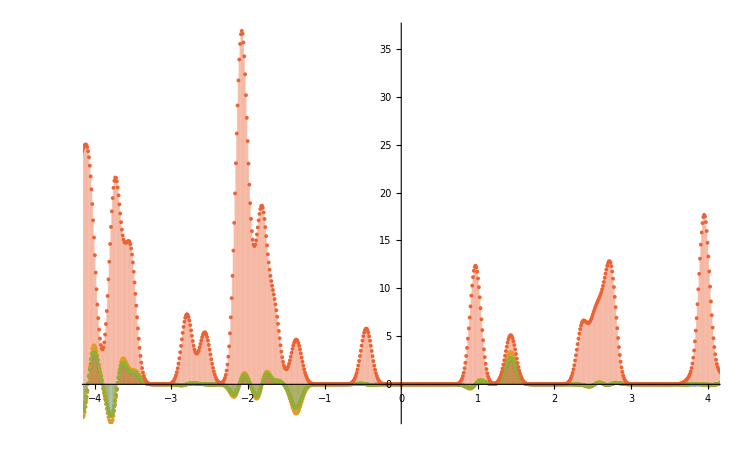

```mathematica
ListPlot[{Table[Tooltip[dosesmoldn2[[i]],i],{i,1,Length[dosesmoldn2]}],Table[Tooltip[dosesmolmi2[[i]],i],{i,1,Length[dosesmoldn2]}],Table[Tooltip[dosesmolup2[[i]],i],{i,1,Length[dosesmoldn2]}],Table[Tooltip[dosesmolall2[[i]],i],{i,1,Length[dosesmoldn2]}]},Filling->Axis,Joined->False,PlotRange->{{-4,4},{Min[dosesmoldn2[[All,2]]],Max[dosesmolall2[[All,2]]]}},ImageSize->750]
```

Visualization

```mathematica
type="sp";(*"so";*)  (* Type of calculations: "sp"=Spin-polarized; "so"=spin-orbit coupling *).1c
spin="all";(*"up";*)(*"down";*)(*"x";*)(*"y";*)(*"z";*)  (* Which spin to visualize *)
first=134;
last=142;
If[(spin=="up" )||( spin=="x"),{Do[{doses[i]=Abs[dosesup[i][[All,2]]]},{i,maxat1}],Print["up or x"]},If[(spin=="down") ||( spin=="z"),{Do[{doses[i]=Abs[dosesdn[i][[All,2]]]},{i,maxat1}],Print["down or z"]},If[( spin=="y"),{Do[{doses[i]=Abs[dosesmi[i][[All,2]]]},{i,maxat1}],Print["y"]},{(*spin=="all"*)Print["all"],If[type=="sp",{Do[{doses[i]=Abs[dosesup[i][[All,2]]]+Abs[dosesdn[i][[All,2]]]},{i,maxat1}],Print["sp"]},(*type=="so"*){Do[{doses[i]=Abs[dosesall[i][[All,2]]]},{i,maxat1}],Print["so"]}]}]]];
max=0.0;
For[i=1,i≤maxat1,i++,{dosessum[i]=Total[doses[i][[Range[first,last,1]]]],If[dosessum[i]>max,max=dosessum[i]]}];
max
For[i=1,i≤maxat1,i++,{dosessum[i]=dosessum[i]/max}]

rescale2 = 0.4;
color=(*"TemperatureMap"*)"DarkRainbow";
With[{c=ColorData[color]},
geom03=Table[{Opacity[dosessum[i]],(*Darker[Blue,.3]*)c[dosessum[i]],Sphere[geom[[i,{3,4,5}]],rescale2*geom[[i,6]]]},{i,1,maxat1}]];
expo=Graphics3D[{geom03,balls,sticks},Lighting->"Neutral",ViewPoint->20000. {0,-1,1},ImageSize->1000,Axes->False,Boxed-> False,Background->None]
```

.1c

all

sp

3.94836

-Graphics3D-

```mathematica
Export[path<>"???_state.png",expo,Background->None]
```

```mathematica
expo=.
```

```mathematica
Do[{dosessum[i]=.;doses[i]=.},{i,maxat1}]
```